```mathematica
Clear["Global`*"]
```

### Underdamping

```mathematica
x[t_]:=Exp[-g t/2](A0 Cos[Sqrt[w0^2-g^2/4]t])
```

```mathematica
With[{f=x[t]},Manipulate[{w0^2-g^2/4>0,Plot[f,{t,0,50},ImageSize->Medium,PlotRange->All]},{{A0,0},0,4},{{g,0},0,4},{{w0,0},0,8}]]
```

### Overdamping

```mathematica
y[t_]:=A Exp[-(g/2-Sqrt[g^2/4-w0^2])t]+B Exp[-(g/2+Sqrt[g^2/4-w0^2])t]
```

```mathematica
With[{f=y[t]},Manipulate[{g^2/4-w0^2>0,g/2-Sqrt[g^2/4-w0^2],Plot[f,{t,0,50},PlotRange->All,ImageSize->Medium]},{A,-2,8},{B,0,2},{g,0,16},{w0,0,2}]]
```

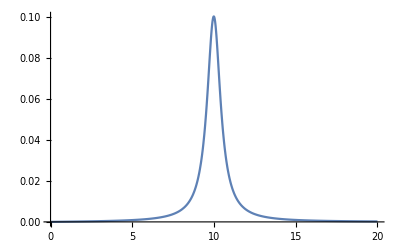

```mathematica
Plot[w/((w0^2-w^2)^2+w^2)/.{w0->10},{w,0,20},PlotRange->All]
```

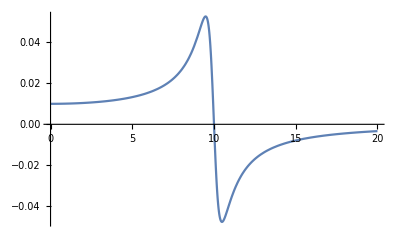

```mathematica
Plot[(w0^2-w^2)/((w0^2-w^2)^2+w^2)/.{w0->10},{w,0,20},PlotRange->All]
```

```mathematica
Solve[D[(w0^2-w^2)/m/((w0^2-w^2)^2+g^2w^2),w]==0,{w}]
```

{{w→0},{w→-√w0 √(g+w0)},{w→√w0 √(g+w0)},{w→-√(-g w0+w0^2)},{w→√(-g w0+w0^2)}}